## Simulating NV carbon evolution from pulses

### Basic setup

```mathematica
Quiet[Needs["QDENSITY`Qdensity`"]];
(*?QDENSITY`Qdensity`**)
```

Type "?intro", "?QDENSITY`Qdensity`*" or "?about for help.

General useful definitions such as gates etc.

```mathematica
KP[r__]:=KroneckerProduct[r]
ρfromψ[ψ_] :=ψ.ψ†;
MixedState=𝕀/2;(*Mixed state*)

transformAndNorm[state_,U_]:=(out=U.state.U†;out=out/Tr[out]);
norm[state_]:=state/Tr[state];
transform[state_,U_]:=U.state.U†;
measureOut[state_]:=KP[Subscript[𝒫, 0],Subscript[σ, 0]].state.KP[Subscript[𝒫, 0],Subscript[σ, 0]]†+KP[Subscript[𝒫, 1],Subscript[σ, 0]].state.KP[Subscript[𝒫, 1],Subscript[σ, 0]]†;
measureOutAndBranch[state_,U0_,U1_]:=U0.KP[Subscript[𝒫, 0],Subscript[σ, 0]].state.KP[Subscript[𝒫, 0],Subscript[σ, 0]]†.U0†+U1.KP[Subscript[𝒫, 1],Subscript[σ, 0]].state.KP[Subscript[𝒫, 1],Subscript[σ, 0]]†.U1†;
```

```mathematica
(*Single qubit gates*)
{rxp,rXp,ryp,rYp,rzp,rZp}=Table[AF[MatrixExp[-ⅈ*Subscript[σ, Floor[j/2-0.01]+1]*π/(2*(1+Mod[j,2]))]],{j,1,6}];
{rxm,rXm,rym,rYm,rzm,rZm}=Table[AF[MatrixExp[ⅈ*Subscript[σ, Floor[j/2-0.01]+1]*π/(2*(1+Mod[j,2]))]],{j,1,6}];
rThetaX[θ_]=MatrixExp[-ⅈ*Subscript[σ, 1]*θ/2];
rThetaY[θ_]=MatrixExp[-ⅈ*Subscript[σ, 2]*θ/2];
rThetaZ[θ_]=MatrixExp[-ⅈ*Subscript[σ, 3]*θ/2];
rThetaϕ[θ_,ϕ_]=MatrixExp[-ⅈ*(Cos[ϕ] Subscript[σ, 1]*θ+Sin[ϕ] Subscript[σ, 2]*θ)/2];
```

The system Hamiltonian with NV and Carbon is defined below. The carbon params are constrained to automatically satisfy the carbon calibrations for precession under ms=0 and ms=1, as long as ω0 and ω1 are the same as in msmt_params.

```mathematica
CarbonParams[ω0_,ω1_,Apar_]:=
{ω0,Apar+ω0,Sqrt[(ω1)^2-(Apar+ω0)^2]};
```

```mathematica
Usys[t_,{ω_,par_,Aperp_}] := MatrixExp[-ⅈ t/2(ω KP[Subscript[𝒫, 0],Subscript[σ, 3]]+KP[Subscript[𝒫, 1],(par Subscript[σ, 3]+Aperp*Subscript[σ, 1])])];
```

Pull in pulse sequences from file

```mathematica
getPulses[basedir_,measname_]:=Module[{filename,x,attrs,seqOverview,PulseSeqs},
filename=If[FileExtension["filename"]=="",measname<>".h5",measname];
seqOverview={};
attrs={"seq_overview/name","seq_overview/trigger_wait","seq_overview/goto_target","seq_overview/jump_target","seq_overview/final_time"};
For[x=1,x≤Dimensions[attrs][[1]],x++,AppendTo[seqOverview,Import[basedir<>filename,{"Datasets",attrs[[x]]}]]];
seqOverview=Transpose[seqOverview];
PulseSeqs={};
For[x=0,x<Dimensions[seqOverview][[1]],x++,AppendTo[PulseSeqs,Import[basedir<>filename,{"Datasets","pulses/"<>ToString[x]}]]];
seqOverview=Transpose[seqOverview];
Transpose[{Transpose[seqOverview],PulseSeqs}]]
```

Compiler!

Each pulse has a few params:
1.) Centre of pulse
2.) Pulse duration (less useful here)
3.) Phase angle of pulse - for some reason, in the compiled sequences, 0 encodes Y gate, π/2 encodes X gate, 3 π/2 encodes - X gate, π encodes - Y gate
4.) The rotation angle (basically pi/2 or pi)
5.) Special. 1 is repump, 2 is readout (readout is not implemented in all of the datasets, but is also not necessary)

The pulse seq also has some extra data, like what it jumps to, and most importantly, the total length of the pulse sequence.

```mathematica
compiledPulse[{ω_,Apar_,Aperp_},pulseData_,ignoreFinal_:False,triggerReadout_:False,readoutVal_:0]:=Module[{i,numPulses,evMat,pulseMat,pulseDelay,compiledPulse},
numPulses=Dimensions[pulseData[[2]]][[1]];
compiledPulse=IdentityMatrix[4];
For[i=1,i<=numPulses,i++,
pulseDelay=If[i==1, pulseData[[2,i,1]],(pulseData[[2,i,1]]-pulseData[[2,i-1,1]])];
evMat=Usys[pulseDelay,{ω,Apar,Aperp}];
pulseMat=Which[pulseData[[2,i,5]]==0,KP[rThetaϕ[pulseData[[2,i,4]],(π/2-pulseData[[2,i,3]])],Subscript[σ, 0]],pulseData[[2,i,5]]==1,KP[Subscript[𝒫, 0],Subscript[σ, 0]],pulseData[[2,i,5]]==2,If[triggerReadout,KP[Subscript[𝒫, readoutVal],Subscript[σ, 0]],KP[Subscript[σ, 0],Subscript[σ, 0]]]];
compiledPulse=pulseMat.evMat.compiledPulse;
];
pulseDelay=If[Not[ignoreFinal],(pulseData[[1,5]]-pulseData[[2,-1,1]]),0];
compiledPulse=Usys[pulseDelay,{ω,Apar,Aperp}].compiledPulse;
Return[compiledPulse]
]
```

### System parameters

```mathematica
basedir = "/Users/humphreys/Repositories/personal_calcs/Work/Modelling/PulseSim/LT4/";
```

Our nuclear spin parameters:

```mathematica
ω0 = 2π 443172.12;
ω1=2π 416572.34;
Apar =-2*π*(33.0)*10^3 +34349.1; 

CarbonPm=CarbonParams[ω0,ω1,Apar];
```

### Carbon calib

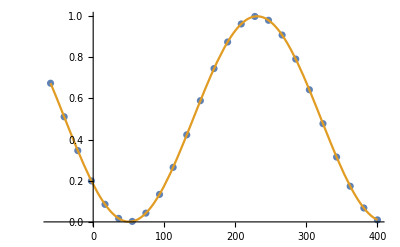

129.55

```mathematica
phaseCalibSeq=getPulses[basedir,"AWG_seqs_phase_C4"];

numPoints =Dimensions[phaseCalibSeq][[1]]/3;
phase=-60+Range[0,numPoints-1]*(460./(numPoints-1));
MeasVals =Module[{i,MeasVals},
MeasVals={};
For[i=1,i≤numPoints,i++,
InitPulse=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[CarbonPm,phaseCalibSeq[[3(i-1)+2]]];
MeasPulse=compiledPulse[CarbonPm,phaseCalibSeq[[3(i-1)+3]]];
pulse=MeasPulse.InitPulse;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{2},transformAndNorm[initState,pulse]];
MeasVals=Append[MeasVals,Tr[Subscript[𝒫, 0].outState]];];
MeasVals];
Clear[x,a];
nlm=NonlinearModelFit[Transpose[{phase,MeasVals}],Amp*Cos[2π (f x+a/360)]+off,{{f,1/360},{a,0},{Amp,1},{off,0.5}},x];
plot2 =Show[ListPlot[{Transpose[{phase,MeasVals}]},Joined->{False}],Plot[Normal[nlm],{x,phase[[1]],phase[[-1]]},PlotStyle->{ColorData[97,"ColorList"][[2]]}]]
aout=If[Amp>0,Mod[a,360],Mod[a+180,360]]/.nlm["BestFitParameters"]
```

### Swap gate (from purification)

```mathematica
SwapX=getPulses[basedir,"AWG_seqs_pur_Swap_el_to_C_X"];
```

```mathematica
SwapY=getPulses[basedir,"AWG_seqs_pur_Swap_el_to_C_Y"];
```

```mathematica
SwapZ=getPulses[basedir,"AWG_seqs_pur_Swap_el_to_C_Z"];
```

Ok, setup the different bits of the sequence!

```mathematica
SwapX[[;;,1]]
```

(C_Init4_y_pt0_tau_0_N_0 | 1 | C_Init4_y_pt0_tau_0_N_0 | LDE10 | 0.000977248
LDE10 | 0 | C_Init4_y_pt0_tau_0_N_0 | Tomo_y_pi2_init0_tau_0_N_0 | 0.000985448
Tomo_y_pi2_init0_tau_0_N_0 | 0 | None | None | 0.000456568
C_Init4_y_pt1_tau_0_N_0 | 1 | C_Init4_y_pt1_tau_0_N_0 | LDE11 | 0.00143182
LDE11 | 0 | C_Init4_y_pt1_tau_0_N_0 | Tomo_y_pi2_init1_tau_0_N_0 | 0.000985448
Tomo_y_pi2_init1_tau_0_N_0 | 0 | None | None | 0.000456004
C_Init4_y_pt2_tau_0_N_0 | 1 | C_Init4_y_pt2_tau_0_N_0 | LDE12 | 0.00143125
LDE12 | 0 | C_Init4_y_pt2_tau_0_N_0 | phase_gate_Tomo4_Ren_a_211_2_tau_0_N_0 | 0.000985448
phase_gate_Tomo4_Ren_a_211_2_tau_0_N_0 | 0 | None | None | 0.000890228)

```mathematica
InitC=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[CarbonPm,SwapZ[[1]]];

InitEAndSwapX=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[CarbonPm,SwapX[[2]]];
InitEAndSwapY=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[CarbonPm,SwapY[[2]]];
InitEAndSwapZ=KP[Subscript[𝒫, 0],Subscript[σ, 0]].compiledPulse[CarbonPm,SwapZ[[2]]];

InitSwap={InitEAndSwapX,InitEAndSwapY,InitEAndSwapZ};

TomoX=compiledPulse[CarbonPm,SwapZ[[3]]];
TomoY=compiledPulse[CarbonPm,SwapZ[[6]]];
TomoZ=compiledPulse[CarbonPm,SwapZ[[9]]];

TomoSwap={TomoX,TomoY,TomoZ};
```

Init sets the carbon to Z

```mathematica
pulse=InitC;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{1},transformAndNorm[initState,pulse]]
```

(0.998532+0. ⅈ | -0.0295592-0.0199572 ⅈ
-0.0295592+0.0199572 ⅈ | 0.00146845+0. ⅈ)

How does it look in different tomo bases?

```mathematica
bases={"X","Y","Z"};
For[j=1,j≤3,j++,Print["Input: "<>bases[[j]]];For[i=1,i≤3,i++,
pulse=TomoSwap[[i]].InitSwap[[j]].InitC;
initState=KP[Subscript[𝒫, 0],Subscript[σ, 0]/2];
outState=PTr[{2},transformAndNorm[initState,pulse]];
Print[bases[[i]]<>" "<>ToString[Re[Tr[Subscript[σ, 3].outState]]]]]]
```

Input: X

X -0.00241272

Y -0.070201

Z 0.992431

Input: Y

X 0.0125593

Y 0.997014

Z 0.101344

Input: Z

X -0.999508

Y 0.0136355

Z -0.0631276